```mathematica
(****
TEMPLATE FOR ITERATIVE OPTIMIZATION ALGORITHMS
Zicheng Gao
 ****)
```

```mathematica
(*** Iteration Settings ***)
InitIterationSettings[]:=(
(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;
doPoint=True;
doGraph=False;
doEPlot=True;
showAll=False;

(** Adaptivity **)
BoostRatio=1.05;
RefineRatio=0.8;
MaxCorrections=50;
ErrorRatio=1.0;

(* Acceleration *)
AccelBoost=1.;
AccelRefine=1.;
AccelAmt=0.00;

showMistakes=False;
fps=0;

(* Tracker values *)
historyAmt=50;
RefreshInterval=50;
);
InitIterationSettings[];
```

```mathematica
InitFunctionData[steepness_,sharpness_,paramVariance_,manualTrueParams_,noiseFactor_, noiseDistribution_,forceData_]:=(
Clear[eFunc,params];
ParamVariance=paramVariance;

(*If we are forcing data, use data, otherwise generate data*)
If[Length[forceData]>0,
Data=forceData;
DataLength=Length[Data];
SamplingSet=N@Range@DataLength/N@SamplingRate;
(* Else *),
SamplingSet=N@Range@DataLength/N@SamplingRate;
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-paramVariance,paramVariance},varamt]];
(* Data Generation *)
NoiselessData=((Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet));
AddNoise=(#+noiseFactor*RandomVariate[noiseDistribution])&;
Data=AddNoise/@NoiselessData;
];

DataN=Norm@Data;
Data=Normalize@Data;
params=Table[Unique["p"],{varamt}];paramh=Hold@@params;

(*Data is already normalized.*)
Angdif[v_,w_]:=(If[Norm@v==0||Norm@w==0,Return@(0)];N@v.w/(Sqrt[N@v.v]*Sqrt[N@w.w]));
Κ=steepness;Q=sharpness;AngMap[x_]:=Κ((x-1)^2+1-Exp[-Q(x-1)^2])/5;
eFunc=paramh/._[vars__]:>Function[{vars},AngMap@N[Angdif[(Normalize[((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)]),Data]]];
);
FindError[]:=(AError=(Total[(((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet)-DataN Data)^2]/(DataLength-varamt))^0.5;);
(*** Global Iteration Reset / Initialize ***)
InitIterationData[factorx_,manualParams_]:=(
totalIter=0;
factor=factorx;

Corrections=0;
ConsecCorrections=0;

(*History*)
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams={iterParams};
err=eFunc@@iterParams;
prevErr=err+1.;

debugErr={err};
doPerturb=False;
FindError[];
);
LinePlot[points_, size_,amount_]:=Show[ListPointPlot3D[{If[amount>0&&size>amount,points[[-amount;;-1]],points]},PlotRange->All,ImageSize->Medium],Graphics3D@Line@If[amount>0&&size>amount,points[[-amount;;-1]],points]];
Default[RefreshSPlot,1]="Speed";
RefreshSPlot[goal_.]:=Module[{dims=Take[#,2]&/@debugParams},
If[varamt≠2,Return[False]];
SPlot=Evaluate@ContourPlot[
eFunc@@{x,y,0},
Evaluate@({x,-1.+Min@#,1.+Max@#}&@(First/@dims)),
Evaluate@({y,-1.+Min@#,1.+Max@#}&@(Last/@dims)),
PlotLegends->Automatic,PerformanceGoal->goal,ImageSize->300,PlotRange->All];];
SLinePlot[points_,size_,amount_]:=Show[SPlot,Graphics@Line@(If[amount>0&&size>amount,points[[-amount;;-1]],points])];
Visualize[]:=
Dynamic@Grid[{
{"Data vs Function","Parameter Space","Error over iterations"},
{ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,DataN Data},Joined->True,ImageSize->Medium,PlotLegends->None],
If[doPoint,Which[
varamt==3,LinePlot[debugParams,totalIter,historyAmt],
varamt==2,SLinePlot[debugParams,totalIter,historyAmt],
True,"Incorrect dimensionality"],"Disabled"],
If[doEPlot,ListLogLogPlot[debugErr,ImageSize->Medium,PlotRange->All],"Disabled"]},
{"Parameters","Iterations, corrections, α, β, LSTolerance, factor"},
{If[showAll||varamt<5,Column[{iterParams}],"Displaying parameters would take too much space."],
Column[{{totalIter,Corrections},{ProgressIndicator[ConsecCorrections/MaxCorrections],α,β},{LSTol,factor}}],
{AError,prevErr}}
},Frame->All,ItemSize->30];
AddToHistory[]:=(debugParams=Append[debugParams,iterParams];debugErr=Append[debugErr,err];);
ToSpacedString=Function[str,StringDrop[StringJoin@@((ToString[#]<>" ")&/@str),-1]];

(*Golden Ratio Search*)
Default[GoldenRatioSearch,8]=False; (* Verbose *)
Default[GoldenRatioSearch,9]=0; (* Constrain iterations *)
GoldenRatioSearch[coeff_,init_,d_,surface_,tolerance_,min_,LSTemp_,verbose_.,max_.]:=Module[{
gr=N@GoldenRatio,f=coeff,l=coeff-LSTemp,h=coeff+N@GoldenRatio*LSTemp,g=coeff+N@GoldenRatio*LSTemp-LSTemp,
e=surface@@(init+#*d)&,i=0,eg,ef,eh,el,
goLeft,goRight,trials=If[verbose,{}]},
While[Abs[f-g]>tolerance&&(max==0||(max≠0&&i++<max)),
If[verbose,trials=Append[trials,{l,f,g,h}]];
eg=e@g;ef=e@f;eh=e@h;el=e@l;
If[eh<ef&&eh<eg,h+=(h-l)*gr;,(* Imbalanced *)
If[el<ef&&el<eg,l=l-gr (h-l),
If[ef<eg,h=g,l=f](* No Problems *)];];
f=h-(h-l)/gr;g=l+(h-l)/gr;
];
If[verbose,trials=Append[trials,{l,f,g,h}];Return@trials,Return@f];
];

RefineFactor[f_]:=(f*=RefineRatio^AccelRefine;ConsecCorrections++;Corrections++;AccelRefine+=AccelAmt;AccelBoost=1.;Return@f);
BoostFactor[f_,ceil_]:=(ConsecCorrections=0;f*=BoostRatio^AccelBoost;AccelRefine=1.;If[f>ceil,Return@ceil]AccelBoost+=AccelAmt;Return@f);

Default[RandomDirection]=1.;
RandomDirection[m_.]:=Module[
{v=ConstantArray[0,varamt]},
While[Norm@v==0,v=Normalize[RandomReal[1.,varamt]]];
Return[v*m];
];
RandomPerp[to_]:=Module[
{v=ConstantArray[0,varamt],m=Norm@to},
While[Norm@v==0,v=RandomDirection[m];v=v-to*v.Normalize@to];
Return[Normalize@v*m];
];

PolyN[degree_]:=Total@(Array[Slot,degree+1,2]*Flatten@MapIndexed[#1^(#2-1)&,Slot/@ConstantArray[1,degree+1]]);

(* Random Walk Combined with Pattern Search and Line Search *)
Iterate[n_,tolerance_,factor_,temp_,prate_,pmax_]:=Module[{
i=0,
ω=factor,
heat=temp},(
While[(i<n &&(NoErr||(AError>tolerance))),
If[doPoint&&varamt==2&&Mod[totalIter,RefreshInterval]==0,RefreshSPlot["Speed"];];

(*We try a perpendicular direction*)
adir=RandomDirection[];
bdir=RandomPerp@adir;
err=eFunc@@iterParams;
α=(Last@(IGRSA=GoldenRatioSearch[ω,iterParams,adir,eFunc,LSTol,err,heat,True]))[[2]];
β=(Last@(IGRSB=GoldenRatioSearch[ω,iterParams,bdir,eFunc,LSTol,err,heat,True]))[[2]];

If[eFunc@@(iterParams+α adir)<eFunc@@(iterParams+β bdir),
δ=β;dir=bdir;iterParams+=β bdir,
δ=α;dir=adir;iterParams+=α adir];

If[eFunc@@iterParams>err,
ConsecCorrections++;Corrections++;
iterParams-=δ dir;
heat*=0.5;ω*=0.667;
,
ConsecCorrections=0;
ω=Min[factor,1.5 ω];heat=Min[temp,2.0 heat];
AddToHistory[];i++;totalIter++;
If[fps≠0,Pause[fps];];
FindError[];
];
]
)];

HDFD[index_]:=Abs@Fourier[Data*Exp[2I π(index-2)N@(Range@DataLength-1)/DataLength],FourierParameters->{0,2/DataLength}];
FindMax[list_]:=Position[list,Max@list][[1,1]];
FindIndexFreq[index_]:=N@((#-2+2(FindMax@HDFD@#-1)/DataLength)*2π*SamplingRate/DataLength)&/@index;
RecoverIndices[]:=First/@(Take[#,Round[(Length@#)/2.]]&@FindPeaks@Abs@Fourier@Data);
RecoverFreqList[]:=(Select[RecoverIndices[],#>0&]//FindIndexFreq);
RecoverDataFreq[i_]:=If[i≤Length@#,#[[i]],#[[Length@#]]]&@RecoverFreqList[];
```

```mathematica
RecordedComparisonData={};
```

```mathematica
(* SET DATA *)
varamt=2;
DataLength=50;
SamplingRate=50;
doNormalize=False;
Fitfunction=Exp[#1 #2]+#3&;
InitFunctionData[5.,512.,5.,{1.,1.},0.,NormalDistribution[1,0.2],{}];
TrueParams
```

{1.,1.}

```mathematica
(* BEGIN ITERATION *)
Smoothness=1;
SmoothingFunction[l_]:=Total[MapIndexed[#1 /2.^First[#2]&,l]]/Smoothness;

RefreshInterval=100;
InitIterationSettings[];
showMistakes=False;
doSteepest=True;

showAll=True;
historyAmt=0;
LSTemp=0.005;
LSTol=0.001;

InitIterationData[0.01,{0.5, 2.}];
RefreshSPlot["Speed"];
doPerturb=False;
Column[{
Visualize[],
ToSpacedString@{"Frequency indices: ", RecoverIndices[]},
ToSpacedString@{"Data frequencies: ", RecoverFreqList[]},
ToSpacedString@{If[!doNormalize,"Not ",""],"Normalized"},
If[showAll||varamt<5,
Column[{ToSpacedString@{"TrueParams",TrueParams},ToSpacedString@{"InitialParams",iterParams},ToSpacedString@{"FitFunction:",InputForm@Fitfunction}}],
"Displaying parameters would take too much space."
],
ToSpacedString@{"LSTemp and LSTolerance:",LSTemp,LSTol}
}]
```

Frequency indices:  {1}
Data frequencies:  {0.}
Not  Normalized
TrueParams {1., 1.}
InitialParams {0.5, 2.}
FitFunction: Exp[#1*#2] + #3 & 
LSTemp and LSTolerance: 0.005 0.001

```mathematica
(*** Iteration loop ***)
(* Manual, Non-optimal Iteration;
NoErr=False;
ITol=0.01/DataN;
IMin=10.^-9/DataN;
MaxNorm=50;
Iterate[1,ITol,IMin,LSTemp,0.1,2.]//AbsoluteTiming*)
(*Automated iteration - most optimized*)
paramhs=ReleaseHold@List@paramh;
debugParams=Reap[NMinimize[
eFunc@@paramhs,paramhs,
StepMonitor:>Sow@paramhs,
Method->"NelderMead"
]][[2,1]];
debugErr=(eFunc@@#)&/@debugParams;
totalIter=Length@debugParams;
iterParams=Last@debugParams;
FindError[];

RefreshSPlot["Quality"];
```

```mathematica
(** Data Recording **)
RecordedComparisonData=Catenate[{RecordedComparisonData,
{{{"Smoothness",Smoothness},
debugErr,debugParams,TotalRefines,
{"Balance",Balance},{"Impatience",Impatience},{"Iterations",totalIter}}}}];
```

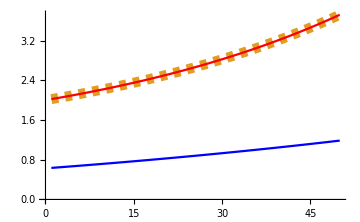

```mathematica
(***Diagnostic Tools***)

(*Parameter History*)
Grid[Take[debugParams,-10]];
Column[eFunc @@ #&/@ Take[debugParams,-10]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]];

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{
(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,
(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,
DataN Data},
Joined->True,ImageSize->Medium,PlotStyle->{Blue,{Dashed,Thickness[0.02]},Red}]
```

```mathematica
ListLogLogPlot[
Table[RecordedComparisonData[[sm,2]],{sm,1,Length@RecordedComparisonData}],PlotLegends->SwatchLegend[
Table[Column[Join[
Flatten@ToSpacedString/@RecordedComparisonData[[sm,{1,7,5,6}]],
{ToSpacedString@{"Final error:",Last@RecordedComparisonData[[sm,2]]},
ToSpacedString@{"Corrections:",RecordedComparisonData[[sm,4]]}}]],{sm,1,Length@RecordedComparisonData}],
LegendFunction->"Panel",LegendLayout->"Row"],
PlotLabel->"Inverse power of two gradient smoothing function with various length amounts",
AxesLabel->{"Iterations","Error"},PlotRange->All,ImageSize->1200,Joined->True,PlotMarkers->{Automatic,4}]
```

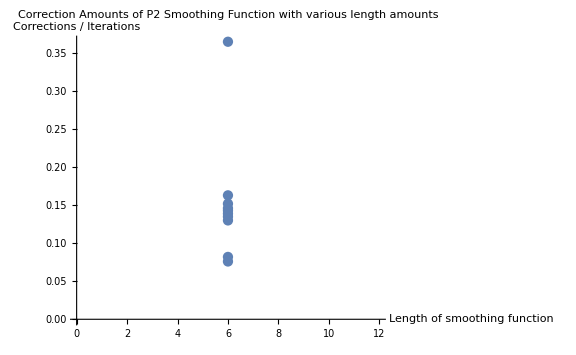

```mathematica
ListPlot[
Table[{RecordedComparisonData[[sm,1,2]],RecordedComparisonData[[sm,4]]/1000.},{sm,1,Length@RecordedComparisonData}],
AxesLabel->{"Length of smoothing function","Corrections / Iterations"},PlotLabel->"Correction Amounts of P2 Smoothing Function with various length amounts",ImageSize->Large]
```

3.2828×10^-6
0.477822
0.000588337
@
{0.444255,-0.374213}
@@
{0.443735,-0.373937}

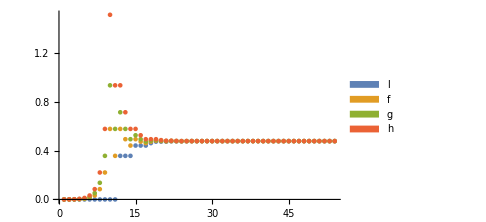
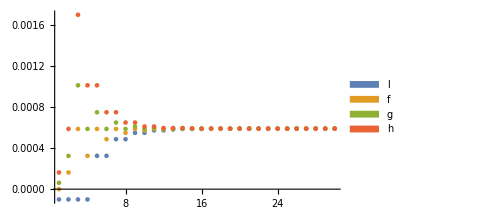
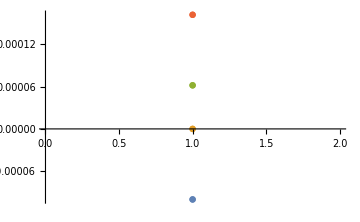
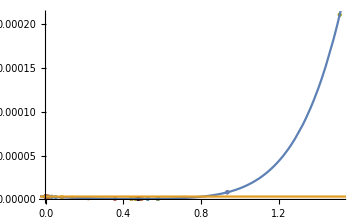
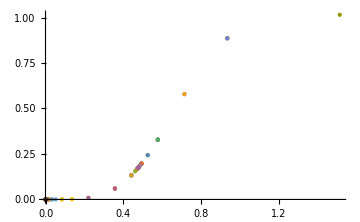
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics-

```mathematica
GRSts=eFunc;
GRSit=iterParams;
GRSa=adir;
GRSb=bdir;
LSTemp=0.0001;
GRSi=0.0000001;
GRStol=0.000000001;
GRSpos=True;
gscale=8;


EFCA=eFunc@@(iterParams+#*adir)&;
EFCB=eFunc@@(iterParams+#*bdir)&;


GRSA=GoldenRatioSearch[GRSi,GRSit,GRSa,GRSts,GRStol,err,LSTemp,True,100];
GRSB=GoldenRatioSearch[GRSi,GRSit,GRSb,GRSts,GRStol,err,LSTemp,True,100];

Column@{err,γ=(Last@GRSA)[[2]],τ=(Last@GRSB)[[2]],"@",iterParams+τ bdir,"@@",iterParams+α adir}
Column[{
Row[{
ListPlot[Transpose@GRSA,PlotLegends->SwatchLegend[{l,f,g,h}],ImageSize->Medium,PlotRange->All],
ListPlot[Transpose@GRSB,PlotLegends->SwatchLegend[{l,f,g,h}],ImageSize->Medium,PlotRange->All],
ListPlot[Transpose@IGRSA,PlotRange->All,ImageSize->Medium],
ListPlot[Transpose@IGRSB,PlotRange->All,ImageSize->Medium]
},Frame->True],
Row[{
Show[ListPlot[Map[{#,EFCA@#}&,GRSA,{2}],PlotStyle->{PointSize@Small,PointSize@Large},ImageSize->Medium,PlotRange->All],Plot[{EFCA@x,err},{x, -gscale γ,gscale γ}],Graphics@Point@{γ,EFCA@γ}],
Show[ListPlot[Map[{#,EFCB@#}&,GRSA,{2}],PlotStyle->{PointSize@Small,PointSize@Large},ImageSize->Medium,PlotRange->All],Plot[{EFCB@x,err},{x, -gscale τ,gscale τ}],Graphics@Point@{τ,EFCB@τ}]
},Frame->True]
}]
```

{}

-Graphics3D-

{1.00111×10^-15,{x→0.999629,y→0.999589}}

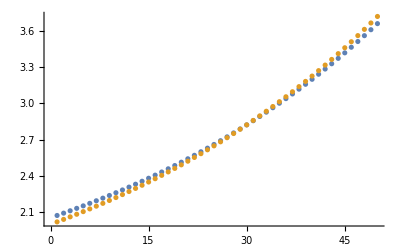

```mathematica
step=0.1;
smin=-2.;
smax=2.;
eSV=Table[Table[{x,y,eFunc[x,y]},{x,smin,smax,step}],{y,smin,smax,step}];
Select[Table[Table[eFunc[x,y],{x,smin,smax,step}],{y,smin,smax,step}],#<0.9&]
ListPlot3D[Flatten[eSV,1],PlotRange->All]

(* Here, we only worry about the value and not the slope. *)
NMinimize[eFunc[x,y],{x,y},Method->"RandomSearch"]
{x,y}/.{x->0.9998573417368651,y->1.1994846729847997};
ListPlot[{DataN Normalize[Fitfunction@@#&/@((Prepend[{1.00018,1.20066},#]&)/@SamplingSet)],Data DataN}]
```

{0.969619,0.244621}

{0.843639,0.536911}

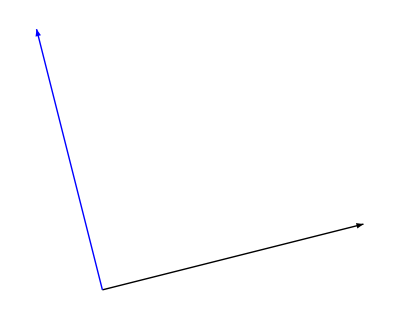

```mathematica
RDIR=RandomDirection[]
RDIT=RandomDirection[]
Graphics@{Arrow@{{0,0},RDIR},Blue,Arrow@{{0,0},RandomPerp[RDIR]}}
```